```mathematica
ΔE[n_,F_]:=-3/2 n(n-1)e a0 F/.{e:>1.6*^-19,a0:>5.29*^-11}
Energy[n_]:=-rydberg/n^2/.{rydberg:>13.6*1.6*^-19}
```

```mathematica
energyLine[n_,F_]:=Energy[n] + ΔE[n,F]
```

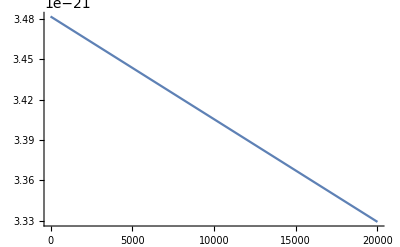

```mathematica
Plot[energyLine[25,F],{F,0,20000}]
```

```mathematica
eqn = (-Subscript[R, ∞] h c)/(n+1)^2-3/2(n+1)n e Subscript[a, 0] F == (-Subscript[R, ∞]h c)/n^2+3/2 n (n-1) e Subscript[a, 0] F
```

-3/2 e F n (1+n) a_0-(c h R_∞)/(1+n)^2==3/2 e F (-1+n) n a_0-(c h R_∞)/n^2

```mathematica
soln = F/.Solve[eqn,F][[1]]
```

(c h (1+2 n) R_∞)/(3 e n^4 (1+n)^2 a_0)

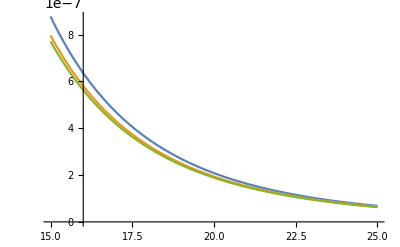

```mathematica
Plot[{2/(3 n^5),soln,orderTerm},{n,15,25}]
```

```mathematica
orderTerm = soln//Expand//Last
```

2/(3 n^3 (1+n)^2)

```mathematica
consts = {c->2.99792458*^8,h->6.62606957*^-34,e->1.60217657*^-19,Subscript[a, 0]->5.2917721092*^-11,Subscript[R, ∞]->10973731.6}
```

{c→2.99792×10^8,h→6.62607×10^-34,e→1.60218×10^-19,a_0→5.29177×10^-11,R_∞→1.09737×10^7}

```mathematica
soln/.{c->2.99792458*^8,h->6.62606957*^-34,e->1.60217657*^-19,Subscript[a, 0]->5.2917721092*^-11,Subscript[R, ∞]->10973731.6}
soln
```

(8.57034×10^10 (1+2 n))/(n^4 (1+n)^2)

(c h (1+2 n) R_∞)/(3 e n^4 (1+n)^2 a_0)

```mathematica
eqnk = (-Subscript[R, ∞] h c)/(n+1)^2-3/2(n+1)n e Subscript[a, 0] F == (-Subscript[R, ∞]h c)/n^2+3/2 n k e Subscript[a, 0] F
```

-3/2 e F n (1+n) a_0-(c h R_∞)/(1+n)^2==3/2 e F k n a_0-(c h R_∞)/n^2

```mathematica
solnk = F/.Solve[eqnk,F][[1]]
```

(2 c h (1+2 n) R_∞)/(3 e n^3 (1+n)^2 (1+k+n) a_0)

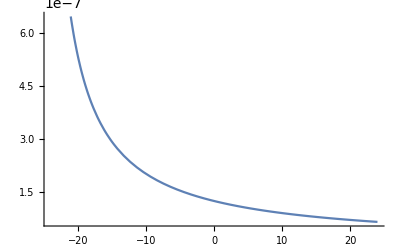

```mathematica
Plot[Evaluate[solnk/.{n->25,c->1,h->1,Subscript[R, ∞]->1,e->1,Subscript[a, 0]->1}],{k,-24,24}]
```

```mathematica
solnk/.consts
```

(1.71407×10^11 (1+2 n))/(n^3 (1+n)^2 (1+k+n))

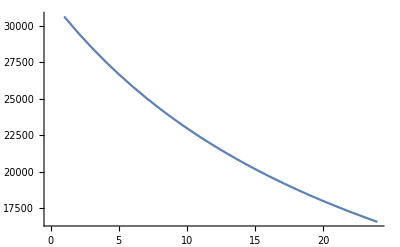

```mathematica
ListPlot[Table[solnk/.consts/.n->25,{k,1,24}],Joined->True]
```

```mathematica
ks[n_,m_]:=Range[-(n-Abs[m]-1),(n-Abs[m]-1),2]
```

```mathematica
Table[{n,ks[n,m]},{n,1,2},{m,-(n-1),(n-1)}]
```

{{{1,{0}}},{{2,{0}},{2,{-1,1}},{2,{0}}}}

```mathematica
MapThread[Prepend,{Table[m,{n,1,10},{m,1,n}],Row[{"n: ",#}]&/@Range[10]}]//Grid
```

n: 1 | 1 |  |  |  |  |  |  |  |  | 
n: 2 | 1 | 2 |  |  |  |  |  |  |  | 
n: 3 | 1 | 2 | 3 |  |  |  |  |  |  | 
n: 4 | 1 | 2 | 3 | 4 |  |  |  |  |  | 
n: 5 | 1 | 2 | 3 | 4 | 5 |  |  |  |  | 
n: 6 | 1 | 2 | 3 | 4 | 5 | 6 |  |  |  | 
n: 7 | 1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  | 
n: 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 |  | 
n: 9 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
n: 10 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

```mathematica
kcounts = Table[Count[Flatten[Table[ks[25,m],{m,-(24),24}]],k],{k,-24,24}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

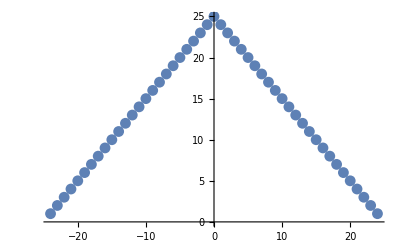

```mathematica
ListPlot[Transpose[{Range[-24,24],kcounts}]]
```

```mathematica
k
```

```mathematica
h
```

```mathematica
TriangularDistribution
```

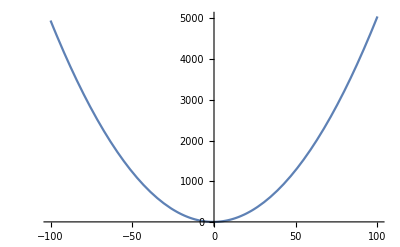

```mathematica
Plot[1/2 n(n+1),{n,-100,100}]
```

```mathematica
real = ImportString["4
13
19
6
6
0
9
5
15
23
16
4
13
5
0
2
5
2
3
10
2
1
0
23
20
17
1
6
11
10
1
10
6
0
3
13
19
1
17
5
8
8
14
2
2
15
17
7
2
7
3
1
8
4
4
1
1
5
13
5
18
15
0
5
2
12
13
13
4
6
6
12
3
4
13
8
0
10
16
7
2
4
3
6
15
4
19
9
12
4
9
11
0
13
11
5
10
6
18
6
7
4
1
3
0
7
8
4
14
10
17
1
17
3
9
5
1
2
5
0
18
11
13
3
2
6
10
0
11
15
6
1
12
10
21
4
12
19
8
18
1
8
9
0
1
4
17
18
6
18
16
3
1
14
11
3
10
6
4
12
4
3
8
4
0
1
15
4
17
18
7
10
4
18
1
5
1
2
14
20
10
18
13
13
10
10
11
3
13
1
12
3
13
10
13
0
1
4
5
17
2
2
8
8
0
16
8
12
12
6
0
2
10
5
4
17
1
16
8
7
10
11
7
2
10
6
3
15
2
1
5
10
18
10
13
2
9
0
14
2
14
1
9
1
10
4
16
10
6
6
3
12
8
6
11
2
10
2
13
15
3
2
9
12
10
11
14
5
19
22
12
17
6
2
17
3
0
8
4
3
9
0
15
2
16
2
2
16
0
5
3
16
0
7
3
21
2
8
13
1
4
7
4
1
7
18
16
12
1
9
1
4
14
1
0
2
13
0
0
10
22
12
10
17
3
6
13
3
14
7
18
4
7
7
7
2
5
0
7
10
9
18
8
10
2
7
8
7
3
10
4
1
10
15
12
8
5
18
0
10
12
11
6
12
3
14
13
22
11
1
1
5
12
15
10
9
18
8
0
7
3
0
8
6
0
7
3
6
17
9
0
8
12
13
15
1
14
17
0
11
5
17
7
7
10
17
17
2
5
7
3
18
18
9
3
6
9
21
18
10
19
1
6
14
5
0
19
0
2
7
4
0
9
2
4
13
16
20
0
4
6
3
6
6
8
1
7
6
18
3
4
12
8
6
16
21
3
4
1
6
16
1
7
16
2
17
5
14
14
11
12
3
2
14
3
4
7
4
6
5
14
15
4
2
16
17
2
10
18
11
14
3
1
8
0
13
4
1
1
3
3
2
4
9
10
8
2
1
0
8
19
21
1
19
10
8
5
3
16
19
17
3
5
6
4
5
13
1
2
4
7
11
11
2
1
6
2
18
6
19
21
11
12
0
6
7
0
16
4
13
16
0
0
3
6
0
14
17
6
7
3
8
3
1
9
7
18
13
6
1
4
6
2
4
6
15
3
7
7
4
2
4
1
5
3
17
17
4
11
14
3
2
7
15
2
1
5
10
1
7
1
20
5
2
11
1
2
14
0
1
3
8
3
20
14
0
17
3
8
19
16
18
6
0
1
3
9
11
23
1
5
11
6
5
20
1
1
9
4
15
9
19
6
8
5
17
10
5
4
1
11
8
11
13
24
6
0
14
1","Table"];
```

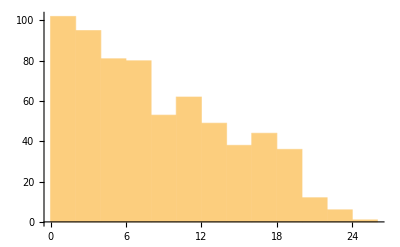

659

```mathematica
Histogram[Flatten@real]
Length@Flatten@real
```

```mathematica
(x-a)(x-b)(x-c)/.x->(b+c)/2//Simplify
```

1/8 (2 a-b-c) (b-c)^2

```mathematica
((x-b)(x-c)+(x-a)(x-c)+(x-a)(x-b))/.x->(b+c)/2//Simplify
```

-1/4 (b-c)^2

```mathematica
f[x_]:=(x-a)(x-b)(x-c)
gamma[x_,x0_]:= f[x0]+f'[x0](x-x0)
```

```mathematica
gamma[x,(b+c)/2]//FullSimplify
f[(b+c)/2]//Simplify
f'[(b+c)/2]//Simplify
```

1/4 (b-c)^2 (a-x)

1/8 (2 a-b-c) (b-c)^2

-1/4 (b-c)^2

```mathematica
(x-b)/.x->(b+c)/2//Simplify
(x-c)/.x->(b+c)/2//Simplify
```

1/2 (-b+c)

(b-c)/2

```mathematica
f[x_]:=k(x-a)(x-b)(x-c)
tangent[fn_,x0_, x_]:=fn[x0]+fn'[x0](x-x0)
midpoint = (a+b)/2;
Reduce[tangent[f,midpoint,c]==0]
```

True